## esempio 1 variabile:

{{y[t]→ⅇ^-t (1+t)}}

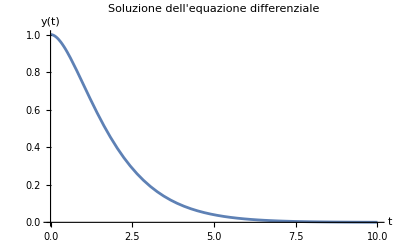

```mathematica
Clear[y,t] (*Pulizia delle variabili*)

(*Definizione dell'equazione differenziale*)
eqn=y''[t]+2 y'[t]+y[t]==0;

(*Condizioni iniziali*)
initialConditions={y[0]==1,y'[0]==0};

(*Risoluzione dell'equazione differenziale*)
sol=DSolve[{eqn,initialConditions},y[t],t]

(*Visualizzazione della soluzione*)
(*Estrazione della soluzione y(t)*)y[t_]=y[t]/. sol[[1]];

(*Plottaggio del grafico della soluzione*)
Plot[y[t],{t,0,10},PlotRange->All,AxesLabel->{"t","y(t)"},PlotLabel->"Soluzione dell'equazione differenziale"]
```

## esempio con 2 variabili:

{{y1[t]→ⅇ^t Cos[t],y2[t]→ⅇ^t Sin[t]}}

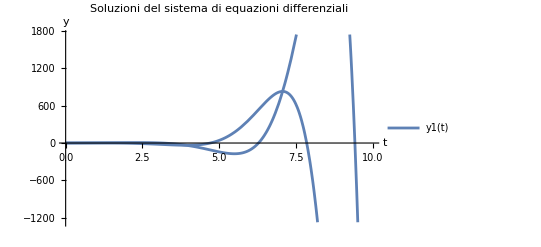

```mathematica
Clear[y1,y2,t] (*Pulizia delle variabili*)

(*Definizione del sistema di equazioni differenziali*)
eqns={y1'[t]==y1[t]-y2[t],y2'[t]==y1[t]+y2[t]};

(*Condizioni iniziali*)
initialConditions={y1[0]==1,y2[0]==0};

(*Risoluzione del sistema di equazioni differenziali*)
sol=DSolve[{eqns,initialConditions},{y1[t],y2[t]},t]

(*Plottaggio delle soluzioni*)
Plot[{y1[t],y2[t]}/. sol,{t,0,10},PlotLegends->{"y1(t)","y2(t)"},AxesLabel->{"t","y"},PlotLabel->"Soluzioni del sistema di equazioni differenziali"]
```

## esempio con NDSolve:

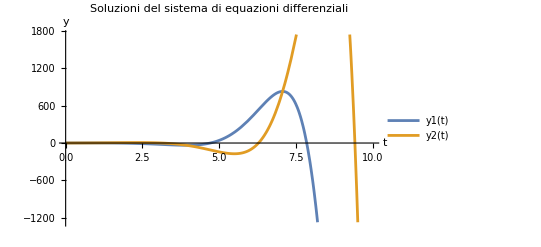

```mathematica
Clear[y1,y2,t] (*Pulizia delle variabili*)

(*Definizione del sistema di equazioni differenziali*)
eqns={y1'[t]==y1[t]-y2[t],y2'[t]==y1[t]+y2[t]};

(*Condizioni iniziali*)
initialConditions={y1[0]==1,y2[0]==0};

(*Risoluzione del sistema di equazioni differenziali*)
sol=NDSolve[{eqns,initialConditions},{y1,y2},{t,0,10}];

(*Plottaggio delle soluzioni*)
Plot[Evaluate[{y1[t],y2[t]}/. sol],{t,0,10},PlotLegends->{"y1(t)","y2(t)"},AxesLabel->{"t","y"},PlotLabel->"Soluzioni del sistema di equazioni differenziali"]
```